```mathematica
pts[x_,y_]:=Flatten[Table[{{1.5n, √3 m+(√3)/2 n},{1.5n+0.5,√3 m+(√3)/2 n+(√3)/2}},{m,-x,x},{n,-y,y}],2];
```

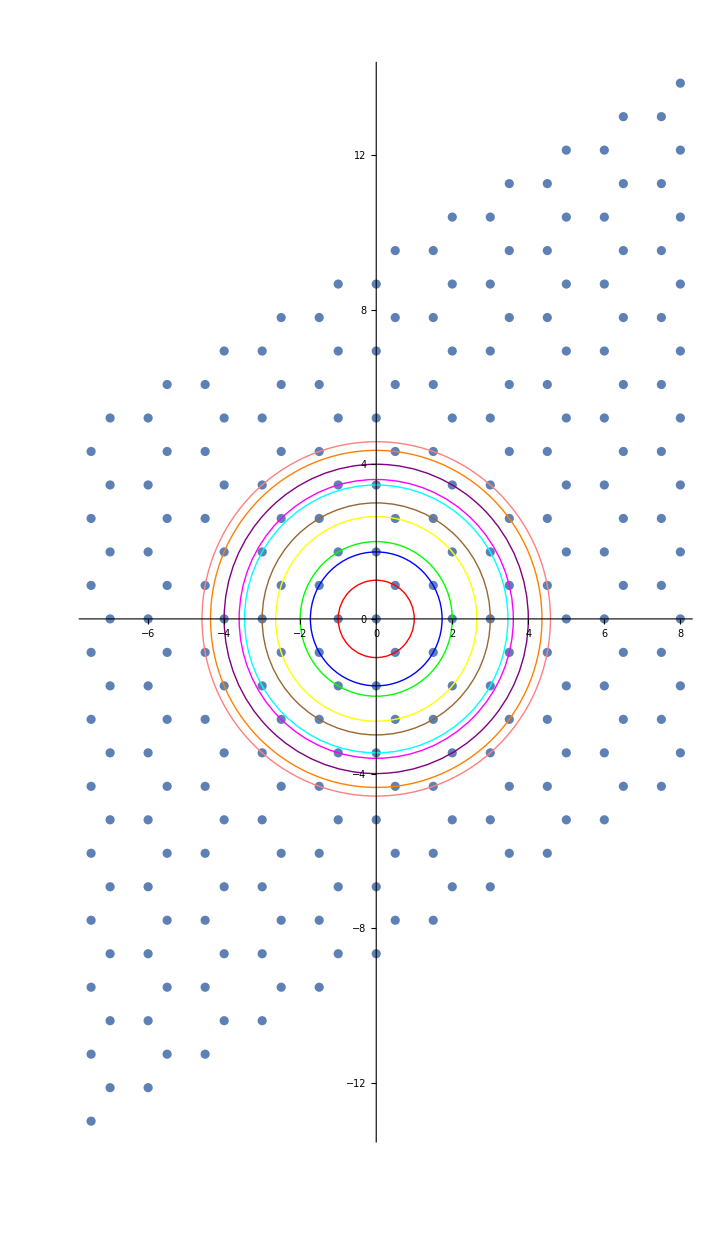

```mathematica
ListPlot[pts[5,5],Epilog->{Red,Circle[{0,0},1],Blue,Circle[{0,0},√3], Green,Circle[{0,0},2], Yellow,Circle[{0,0},√7],Brown,Circle[{0,0},3],Cyan,Circle[{0,0},√12], Magenta,Circle[{0,0},√13], Purple,Circle[{0,0},4],Orange,Circle[{0,0},√19],Pink,Circle[{0,0},√21]},AspectRatio->Equal]
```